# Lecture 16 - Circuit Problems

### A Puzzle...

#### Crash Course in Circuits

Compute the change in voltage from point A to point B (in other words, the voltage difference V_B-V_A) in the following cases. Current of magnitude I flows in the direction given by the blue arrow.

```mathematica
a=-Graphics-;b=-Graphics-;c=-Graphics-;
d=-Graphics-;e=-Graphics-;f=-Graphics-;
centerPlot@Grid[{{a,e,c},{b,f,d}},Spacings->{3,2}]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

Solution
The voltage drop across a resistor is I R in the direction of the current. The voltage drop across a battery is a fixed value (independent of current) which only depends on where the positive and negative terminals are (the positive terminal is represented by the longer line). Therefore, the corresponding voltage differences equal.

```mathematica
ft=Sequence@@{Red,16,FontFamily->"Times"};
a1=Labeled[a,Style[#,ft]&@"V_B-V_A=-IR",Top];
b1=Labeled[b,Style[#,ft]&@"V_B-V_A=+IR",Top];
c1=Labeled[c,Style[#,ft]&@"V_B-V_A=-ℰ",Top];
d1=Labeled[d,Style[#,ft]&@"V_B-V_A=-ℰ",Top];
e1=Labeled[e,Style[#,ft]&@"V_B-V_A=+ℰ",Top];
f1=Labeled[f,Style[#,ft]&@"V_B-V_A=+ℰ",Top];
centerPlot@Grid[{{a1,e1,c1},{b1,f1,d1}},Spacings->{3,2}]
```

-Graphics-V_B-V_A=-IR | -Graphics-V_B-V_A=+ℰ | -Graphics-V_B-V_A=-ℰ
-Graphics-V_B-V_A=+IR | -Graphics-V_B-V_A=+ℰ | -Graphics-V_B-V_A=-ℰ

Any circuit consisting of only resistors and batteries can be analyzed using the above rules. □

### Circuit Problems

```mathematica
centerPlot@-Graphics-
```

-Graphics-

#### Basics

This is your one and only simple circuit problem. Enjoy it while it lasts!

Example
The two circuits below are identical, but we guess that the current travels clockwise on the left-hand side and counter-clockwise on the right-hand side. By considering the voltage drop going clockwise around the circuit, analyze both circuits and determine the magnitude and direction of the current. Then repeat the analysis going counter-clockwise around the circuit.

```mathematica
centerPlot@Grid[{{-Graphics-,-Graphics-}},Spacings->5]
```

-Graphics- | -Graphics-

Solution
On the left-hand circuit, we move clockwise around the circuit. The voltage drop from A to B equals -I_1R, and the voltage drop from C to D equals ℰ. Therefore, the loop equation equals

-I_1R+ℰ=0

so that the current is

I_1=ℰ/R

in the direction shown.

On the right-hand circuit, moving clockwise yields the loop equation

I_2 R+ℰ=0

so that

I_2=-ℰ/R

indicating that we chose the wrong direction for the current (and therefore in agreement with Equation (TextNumbered)).

Repeating the analysis on the left-hand circuit but moving counter-clockwise around the circuit, the loop equation equals

I_1 R-ℰ=0

which is the same result as Equation (TextNumbered) and therefore also yields I_1=ℰ/R.

Lastly, the right-hand circuit moving counter-clockwise yields

-I_2R-ℰ=0

which is the same as Equation (TextNumbered) and yields I_2=-ℰ/R.

As expected, no matter which direction you travel around the circuit and which direction you predict that the current flows, you will find that the current has magnitude ℰ/R and travels clockwise around the circuit.

#### Equivalent Boxes

Example 
A black box with three terminals, a, b, and c, contains nothing but resistors and connecting wire. Measuring the resistance between pairs of terminals, we find R_(a,b)=30Ω, R_(a,c)=60Ω, and R_(b,c)=70Ω. Show that the contents of the box could be either of the configurations shown in the figure below. Is there any other possibility? Are the two boxes completely equivalent, or is there an external measurement that would distinguish between them?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
In the first case we simply have resistors in series so that

R_(a,b)=10Ω+20Ω=30Ω

R_(a,c)=10Ω+50Ω=60Ω

R_(b,c)=20Ω+50Ω=70Ω

as desired. In the second case, the resistance between a and b is the sum of the parallel resistors 34Ω and 85Ω+170Ω=255Ω, which is 1/(R_(a,b))=1/(34Ω)+1/(255Ω)=1/(30Ω) or R_(a,b)=30Ω. Repeating this calculation between all the terminals,

1/(R_(a,b))=1/(34Ω)+1/(85Ω+170Ω)=1/(30Ω)

1/(R_(a,c))=1/(85Ω)+1/(34Ω+170Ω)=1/(60Ω)

1/(R_(b,c))=1/(170Ω)+1/(85Ω+34Ω)=1/(70Ω)

This proves that both of the boxes yield the desired resistances between the terminals.

For the two configurations shown, the above resistances are the only possibility that leads to the given resistances between the terminals. Each configuration yields three equations for the three resistances, so they are uniquely determined. You can prove this to yourself by solving the general system of equations using Mathematica and noting that there is only one solution.

```mathematica
Simplify@Solve[{(R1*(R2+R3))/(R1+R2+R3)==Rab,(R2*(R1+R3))/(R1+R2+R3)==Rac,(R3*(R2+R1))/(R1+R2+R3)==Rbc},{R1,R2,R3}]
```

{{R1→(Rab^2+(Rac-Rbc)^2-2 Rab (Rac+Rbc))/(2 (Rab-Rac-Rbc)),R2→-(Rab^2+(Rac-Rbc)^2-2 Rab (Rac+Rbc))/(2 (Rab-Rac+Rbc)),R3→-(Rab^2+(Rac-Rbc)^2-2 Rab (Rac+Rbc))/(2 (Rab+Rac-Rbc))}}

However, there are other configurations that also work, for example, the one pictured below (as you can check).

```mathematica
centerPlot@-Graphics-
```

-Graphics-

The potential assumed by the free terminal when the potentials at the other two terminals are fixed is the same for the two boxes. For example, if the potentials at b and c in the first box are fixed at ϕ_b and ϕ_c, then

ϕ_b=ϕ_c-I (70Ω)

ϕ_a=ϕ_c-I (50Ω)

Note that no current flows across the 10Ω resistor in this case. Substituting the first equation into the second to get rid of I,

ϕ_a=5/7 ϕ_b+2/7 ϕ_c

Therefore, the potential at a divides the difference ϕ_b-ϕ_c in the ratio of 20 to 50. And in the second box the ratio is 34 to 85, which is the same. The two boxes are therefore indistinguishable by external measurements (using direct currents). You can show that the extra configuration shown above also yields the same ratio of 2 to 5. □

#### Using Symmetry

Example 
This exercise deals with the equivalent resistance R_eq between terminals T_1 and T_2 for the network of five resistors shown below. One way to derive a formula for R_eq would be to solve the network for the current I that flows in at T_1 for a given voltage difference V between T_1 and T_2; then R_eq=V/I. The solution involves rather tedious algebra in which it is easy to make a mistake (although it is quick and painless if you use Mathematica), so we’ll tell you most of the answer:

R_eq=(R_1 R_2 R_3+R_1 R_2 R_4+[?,]+R_2 R_3 R_4+R_5(R_1 R_3+R_2 R_3+[?,]+R_2 R_4))/(R_1 R_2+R_1 R_4+[?,]+R_3 R_4+R_5(R_1+R_2+R_3+R_4))

```mathematica
centerPlot@-Graphics-
```

-Graphics-

By considering the symmetry of the network you should be able to fill in the three missing terms. Now check the formula by directly calculating R_eq in four special cases:

R_5=0

R_5=∞

R_1=R_3=0

R_1=R_2=R_3=R_4=R

Compare your results with what the formula gives.

Solution
First rule of problem solving: Don’t get tricked by purposefully crappy diagrams; draw your own version!

The symmetry becomes much more apparent if we redraw the diagram above as

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Looking at the solution

R_eq=(R_1 R_2 R_3+R_1 R_2 R_4+[?,]+R_2 R_3 R_4+R_5(R_1 R_3+R_2 R_3+[?,]+R_2 R_4))/(R_1 R_2+R_1 R_4+[?,]+R_3 R_4+R_5(R_1+R_2+R_3+R_4))

we see that the first missing term in the numerator must be R_1 R_3 R_4 (the mirror-image of the R_1 R_2 R_3 term) and the second term must be R_1 R_4 (the mirror-image of the R_2 R_3 term). The missing term in the denominator must be R_2 R_3 (the mirror-image of the R_1 R_4 term). Thus, the solution is

R_eq=(R_1 R_2 R_3+R_1 R_2 R_4+R_1 R_3 R_4+R_2 R_3 R_4+R_5(R_1 R_3+R_2 R_3+R_1 R_4+R_2 R_4))/(R_1 R_2+R_1 R_4+R_2 R_3+R_3 R_4+R_5(R_1+R_2+R_3+R_4))

```mathematica
centerPlot@-Graphics-
```

-Graphics-

(a) If R_5=0, we can redraw the diagram as shown above with the middle point collapsed (because it is short-circuited). The parallel combination of R_1 and R_3 is in series with the parallel combination of R_2 and R_4. Thus the resistance equals

R_eq=(R_1 R_3)/(R_1+R_3)+(R_2 R_4)/(R_2+R_4)=(R_1 R_2 R_3+R_1 R_2 R_4+R_1 R_3 R_4+R_2 R_3 R_4)/(R_1 R_2+R_1 R_4+R_2 R_3+R_3 R_4)

which agrees with Equation (TextNumbered) when R_5=0.

(b) If R_5=∞, no current flows through the R_5 edge so we can redraw our circuit as shown above. The series combination of R_1 and R_2 is in parallel with the series combination of R_3 and R_4, so that the resistance equals

R_eq=((R_1+R_2)(R_3+R_4))/(R_1+R_2+R_3+R_4)

which agrees with Equation (TextNumbered) when R_5=∞.

(c) If R_1=R_3=0, then we effectively have the circuit shown above with R_5 short-circuited via R_1 and R_3. Therefore the resistance is simply R_2 and R_4 in parallel,

R_eq=(R_2 R_4)/(R_2+R_4)

in agreement with Equation (TextNumbered) when all terms containing R_1 and R_3 are dropped.

(d) If R_1=R_2=R_3=R_4=R, then by symmetry no current flows through R_5 (equivalently, the current will be split into I/2 going through R_1 and I/2 going through R_3, so that the voltage on either side of R_5 is the same, and therefore no current flows through R_5). Therefore we can redraw the circuit as shown above, with the effective resistance across R_1 and R_3 equal to R/2, and likewise for R_2 and R_4. Therefore, the effective resistance equals

R_eq=R

in agreement with Equation (TextNumbered) in this limit.

More generally, if R_1=R_3=a and R_2=R_4=b, then no current flows through R_5, so we again have two sets of parallel resistors. You should check that the formula agrees with what you calculate directly.

Finally, we can compute Equation (TextNumbered) directly by using the loop equations for the circuit below.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

The three loop equations are

ℰ-(I_3-I_1)R_3-(I_3-I_2)R_4=0
-I_1 R_1-(I_1-I_2)R_5-(I_1-I_3)R_3=0
-I_2 R_2-(I_2-I_3)R_4-(I_2-I_1)R_5=0

Solving these equations using Mathematica,

```mathematica
FullSimplify@Solve[{ℰ-(I3-I1)R3-(I3-I2)R4==0,-I1 R1-(I1-I2)R5-(I1-I3)R3==0,-I2 R2-(I2-I3)R4-(I2-I1)R5==0},{I1,I2,I3}]
```

{{I1→((R3 (R2+R4)+(R3+R4) R5) ℰ)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R2 R3 R4+(R1+R2) (R3+R4) R5),I2→(((R1+R3) R4+(R3+R4) R5) ℰ)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R2 R3 R4+(R1+R2) (R3+R4) R5),I3→(((R1+R3) (R2+R4)+(R1+R2+R3+R4) R5) ℰ)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R2 R3 R4+(R1+R2) (R3+R4) R5)}}

Since I_3 is the current going through the battery,

I_3=ℰ/R_eq

where R_eq is the equivalent resistance that we are looking for. Comparing the form of R_eff thus found by Mathematica, we do indeed see that it is identical to Equation (TextNumbered), as desired. □

### Capacitors

#### Theory

The power delivered to a circuit element at potential difference V with current I flowing through it equals

P=I V=I^2 R

A capacitor has the circuit symbol  and functions by accumulating charge Q until the potential V=Q/C across the capacitor prevents the further flow of current across the capacitor.

One important point to remember is that current never flows between the plates of a capacitor. Rather, current flows from one plate around the circuit into the other plate, leaving the former negatively charged and the latter positively charged. A typical circuit problem will analyze the charging and discharging of a capacitor, and in both cases the current around the circuit eventually slows down to zero.

#### Charging a Capacitor

Example
You can charge up a capacitor by connecting it to a battery of fixed voltage ℰ. Imagine that we hook up an uncharged capacitor to the circuit below at time t=0.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Determine Q[t] and I[t] as functions of time.

Find the total energy output of the battery (∫I[t] ℰⅆt). Determine the heat delivered to the resistor.

What is the final energy stored in the capacitor? What fraction of the work done by the battery shows up as energy in the capacitor? (Notice that the answer is independent of R!)

Solution
1. Let Q[t] be the charge on the capacitor, so that the current I=ⅆQ[t]/ⅆt. The loop equation around the circuit equals

0=ℰ-Q/C-I R
=ℰ-Q/C-ⅆQ/ⅆt R

Solving this differential equation yields

Q[t]=C ℰ+c_1 ⅇ^(-t/(R C))

Upon substituting the initial condition Q[0]=0, c_1=-C ℰ so that

Q[t]=C ℰ(1-ⅇ^(-t/(R C)))

Therefore, the current in the circuit equals

I[t]=ⅆQ[t]/ⅆt=ℰ/R ⅇ^(-t/(R C))

The plot below shows Q[t] and I[t] for the case when ℰ/R>C ℰ. Notice that the capacitor will charge up until its potential asymptotically reaches ℰ, at which point current will stop flowing.

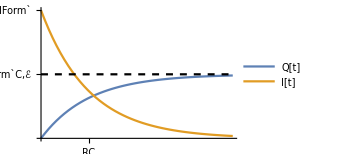

```mathematica
centerPlot@Plot[{1-E^-t,2 E^-t,1},{t,0,4},PlotLegends->{"Q[t]","I[t]"},Ticks->{{{1,"RC"}}, {{1,"TraditionalForm`C,ℰ"},{2,"TraditionalForm`"}}},PlotStyle->{Automatic,Automatic,{Black,Dashed}},ImageSize->250]
```

2. The total energy delivered from the battery equals

W_battery=∫_0^∞ I[t] ℰⅆt
=∫_0^∞ ⅆQ[t]/ⅆt ℰⅆt
=ℰ (Q[∞]-Q[0])
=C ℰ^2

The heat delivered to the resistor equals

W_resistor=∫_0^∞ I[t]^2 Rⅆt
=∫_0^∞ ℰ^2/R ⅇ^(-(2t)/(R C))ⅆt
=1/2 C ℰ^2

3. The energy in a capacitor equals 1/2 Q^2/C. Thus, the capacitor started out with zero energy and through the charging process gained the energy

W_capacitor=1/2 Q[∞]^2/C
=1/2 C ℰ^2

Therefore, half of the battery’s work went into charging the capacitor and half was dissipated by the resistor (there is no free lunch!). It is remarkable that this result is independent of the resistance R! □

#### Advanced Section: A Superconducting Circuit

A very astute reader may have noticed that in the previous problem, the work C ℰ^2 from the battery gets split up half into the resistor and half into the capacitor, regardless of how small R is. But what about the R=0 limit? In that case, there is no resistor, and hence the work C ℰ^2 of the battery goes half into the capacitor and half into...nothing? Is energy not conserved?

First of all, let’s explore how bizarre the R=0 really is. All batteries have some internal resistance, and so would any real capacitor and any other circuit elements. However, you could imagine creating a superconducting circuit using a perfect battery and perfect capacitor where the resistance truly does go to zero. In that case, as soon as you close the switch, the charge Q=C ℰ would instantly be transferred through the circuits between the plates of the capacitor, which implies that there will be an infinite current in that brief instant. As you might imagine, infinite currents are impossible.

But putting all of these issues aside from the moment, let’s just get down to the pure mathematics. Where does the extra energy from the battery go? The answer lies in the fact that any capacitor (even a perfect, no-resistance capacitor) will have some self inductance, a quantity that you will learn about in Ph 1c. When R=0, the circuit above has to be analyzed as an LC-circuit, and in doing so the energy calculation will once again come out to be right. (If you want to analyze the above circuit as an LRC-circuit, it will be even more correct than our calculation, and when L is small and R is large you will regain the same answer we found above.)

A more detail answer given here gives several reasons why superconductors don’t carry infinite current:

Practical Limit No matter what method you use to put a current II into a superconductor, there is a natural limit, which is given by the critical current IcIc. You’ll probably want to design your circuit in such a way that you don’t go over this limit.

AC Limit The resistance of a superconductor is only zero in the stationary case, that is when neither voltages nor currents change. For any AC-signals, it definitely has some resistance! There are several effects that have to be taken into account when minimizing losses in, for example, superconducting LC tank circuits for signal pickup, as it is done in single-ion detectors. You mentioned RC-time constants, this often implies that we are talking about AC-signals, or at least something non-stationary, so there will be some resistance. But it will be low.

DC limit Even in the (almost) stationary case of non-changing currents and voltages, real superconductors have some resistance. The superconducting magnet (a superconducting coil with 30 A of current in it) that I use has a field that decays with a time-constant of a few hundred thousand years, probably due to the weld that joins the superconducting wire to a loop. There seems to be an ongoing debate on whether or not a superconducting loop emits synchrotron radiation, but in any case this would be an extremely small effect that leads to decay constants that are longer than the age of the universe. I guess in real life, cosmic rays knocking the occasional cooper-pair out of order play a much bigger effect.

In the case of a properly designed superconducting capacitor, the resistance of the superconductor is negligible compared to its inductance, which is why an RC description is not a good way to model the system. (Note that even a straight wire has self-inductance, and so does any capacitor, be it superconducting or not.) If you use a more appropriate LC-model to describe your system, you quickly see why the current is limited:

As you start charge your superconducting capacitor, the inductance limits the rate of the current change to ⅆI/ⅆt=U/L, so the current increases until the capacitor is charged. But the current keeps going (due to the inductance!) so that the voltage of the capacitor will be higher than what the voltage source applies. The voltage source will work against the inductance to reverse the current, so that the voltage goes down. Again, as the capacitor is at nominal voltage that the voltage source applies, the current is still going. The voltage across the capacitor will go down further, as the current is reversed again. Basically, by switching on the voltage source you excited a parallel LC circuit, and it will ring forever at its resonance frequency ω=√(L,C).

Really forever? No, the AC-losses will cause the oscillation to die down within 10^3-10^6 periods.

#### Discharging a Capacitor

Example
The book (Section 4.11) describes a the simple RC circuit shown below. Assuming that the capacitor starts off with charge Q_0 and the switch is closed at t=0,

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Q[t]=C V_0 ⅇ^(-t/(R C))

I[t]=-ⅆQ[t]/ⅆt=V_0/R ⅇ^(-t/(R C))

Find the original energy stored in the capacitor. Then integrate the total heat delivered to the resistor over time and verify that this equals the energy lost by the capacitor at any time t.

Solution
Note that the current I[t]=-ⅆQ[t]/ⅆt which is the negative of the relation found in the “Charging a Capacitor” problem above because the capacitor is discharging!

The energy stored in a capacitor equals

U=1/2 Q^2/C=1/2 C V^2

Assume (without loss of generality) that the right plate of the capacitor is positively charged while the left plate is negatively charged, so that current will flow clockwise. The loop equation (written in terms of Q) equals

0=Q/C-I R=Q/C+ⅆQ/ⅆt R

which has the solution

Q[t]=c_0 ⅇ^(-t/(R C))

Using the initial condition Q[0]=Q_0, c_0=Q_0 so that

Q[t]=Q_0 ⅇ^(-t/(R C))

At any time t, the power delivered to the resistor equals

P=I^2 R
=(ⅆQ/ⅆt)^2 R
=Q_0^2/(R C^2)ⅇ^(-(2t)/(R C))

Therefore, the total energy dissipated by the resistor equals

∫_0^t Pⅆt=∫_0^t Q_0^2/(R C^2)ⅇ^(-(2t)/(R C))ⅆt=Q_0^2/(2C)(1-ⅇ^(-(2t)/(R C)))

while the energy lost by the capacitor equals

Δ,U=1/2 Q_0^2/C-1/2 Q[t]^2/C
=1/2 Q_0^2/C-1/2(Q_0^2 ⅇ^(-(2t)/(R C)))/C
=Q_0^2/(2C)(1-ⅇ^(-(2t)/(R C)))

in agreement with Equation (TextNumbered), as expected. □